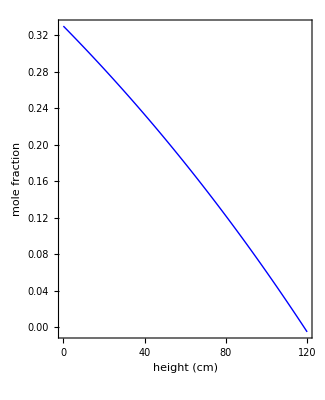
-Graphics- | -Graphics3D-

```mathematica
Module[{r,y,conc,p1,p2},
r=20;
y[x_]:=1-0.67*1.5^(x/120);

conc[x_]:=Rescale[y[x],{y[120],y[0]}];

p1=Plot[y[x],{x,0,120},PlotStyle->{Thick,Blue},PlotRangePadding->None,
Frame->True,FrameLabel->{"height (cm)","mole fraction"},FrameTicks->True,LabelStyle->{17,Black},ImageSize->{325,400},AspectRatio->Full];

p2=ParametricPlot3D[{r*Cos[θ],r*Sin[θ],z},{θ,0,2*Pi},{z,0,120},ColorFunction->(Opacity[conc[#3],Green]&),ColorFunctionScaling->False,
Mesh->None,Boxed->False,Axes->False,ViewPoint->Front,ImageSize->{275,400}];

Grid@{{p1,p2}}
]
```